# Black-body Radiation

General::munfl: Exp[-39127.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.37763×10^35 1.2702583611×10^-16993 is too small to represent as a normalized machine number; precision may be lost.

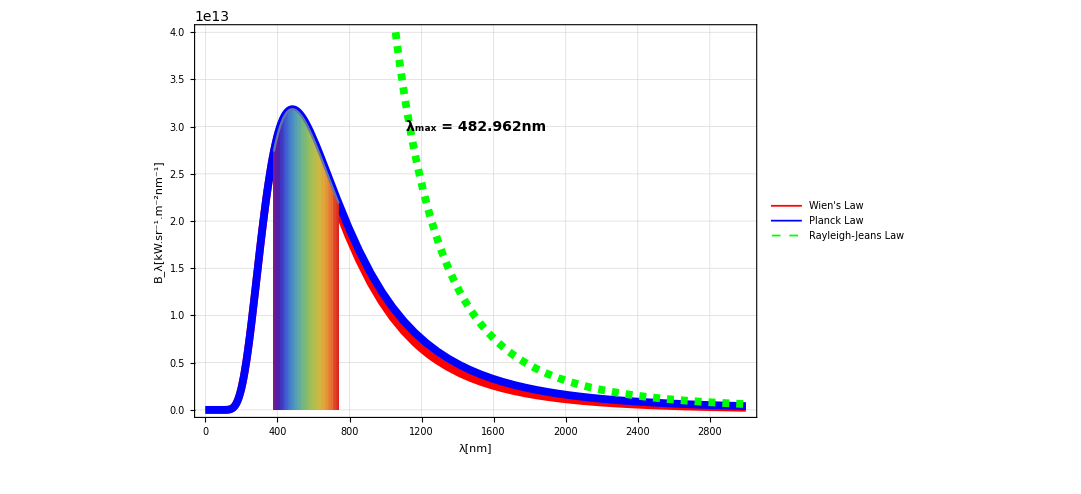

```mathematica
c=299792458;(*m/s*)
T=6000;
k=1.38064852*10^-23;
h=6.62607004*10^-34;
nm=10^-9;
peak = 2.897771955185172*10^-3*10^9/T; (*Wien's Displacement Law*)
B1[λ_] := (2*h*c^2)/λ^5*Exp[-(h*c)/(λ*k*T)]; (*Wien's Approximation*)
B2[λ_]:=(2*h*c^2)/λ^5*1/(Exp[(h*c)/(λ*k*T)]-1);(*Planck's Law*)
B3[λ_]:=(2*c*k*T)/λ^4; (*Rayleigh-Jeans Law*)

fcolor = ColorData["Rainbow"];
m=Show[Plot[{B1[v*nm],B2[v*nm],B3[v*nm]},{v,0,3000},PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Blue,Thickness[0.007]],Directive[Green,Thickness[0.007],Dashed]},PlotLegends->{"Wien's Law","Planck Law","Rayleigh-Jeans Law "},Frame->True,GridLines->Automatic,Epilog->{Text[Style[Row[{"λ_max"," = ",peak,"nm"}],FontSize->14,Bold],{1500,3 10^13}]},FrameLabel->{"λ[nm]","B_λ[kW.sr^-1.m^-2nm^-1]","Black-body Radiation"},LabelStyle->"Subtitle",(*LabelStyle->Directive[Bold, FontSize->30,White],*)ImageSize->{800,600},PlotRange->{{0,3000},{0,4*10^13}}],Plot[B2[v*nm],{v,380,740},PlotStyle->{Red,Blue,Green},Frame->True,GridLines->Automatic,LabelStyle->"Subtitle",(*LabelStyle->Directive[Bold, FontSize->30,White],*)ImageSize->{800,600},Filling->Axis,ColorFunction->Function[{x,y},fcolor[x]],Epilog->{Text[Style[Row[{"λ_max"," = ",peak,"nm"}],FontSize->14,Bold],{1500,3 10^13}]},PlotRange->{{0,3000},{0,10^14}}]]
```